Indeksi cen stanovanjskih nepremičnin po vrstah stanovanjskih nepremičnin, Slovenija, četrtletno

## Pridobivanje prvotnih podatkov iz SURS-a

```mathematica
podatki2=Import[NotebookDirectory[]<>"podatki.csv", "Table", "FieldSeparators"->";", HeaderLines->2, CharacterEncoding->"WindowsEastEurope"]//ResourceFunction["DatasetWithHeaders"]
```

## Primerjava posameznih vrst nepremičnin z njihovimi indeksi po letih za četrtletje Q1 iz prvotne tabele

```mathematica
podatkiSamoQ1=Import[NotebookDirectory[]<>"podatki2.csv", "Table", "FieldSeparators"->";", HeaderLines->3, CharacterEncoding->"WindowsEastEurope"]//Prepend[#,{"Vrsta nepremičnine","2007", "2008", "2009","2010","2011","2012","2013","2014","2015","2016","2017","2018","2019","2020","2021"}]&//ResourceFunction["DatasetWithHeaders"]
```

```mathematica
(*povsod, kjer so bile ..., sem zamenjala z 0 in dodala stolpcem imena*)
```

```mathematica
zNiclo = podatkiSamoQ1//Query[All,<|#, "2007"->If[#"2007"=="...",0,#"2007"],"2008"->If[#"2008"=="...",0,#"2008"],"2009"->If[#"2009"=="...",0,#"2009"],"2010"->If[#"2010"=="...",0,#"2010"],"2011"->If[#"2011"=="...",0,#"2011"],"2012"->If[#"2012"=="...",0,#"2012"],"2013"->If[#"2013"=="...",0,#"2013"],"2014"->If[#"2014"=="...",0,#"2014"],"2015"->If[#"2015"=="...",0,#"2015"],"2016"->If[#"2016"=="...",0,#"2016"],"2017"->If[#"2017"=="...",0,#"2017"],"2018"->If[#"2018"=="...",0,#"2018"],"2019"->If[#"2019"=="...",0,#"2019"],"2020"->If[#"2020"=="...",0,#"2020"],"2021"->If[#"2021"=="...",0,#"2021"]|>&]
```

## Nove stanovanjske nepremičnine

```mathematica
podatki=Import[NotebookDirectory[]<>"podatki2.csv", "Table", "FieldSeparators"->";", HeaderLines->2, CharacterEncoding->"WindowsEastEurope"];
leta=podatki//First//Rest//StringTake[#,4]&//ToExpression//Prepend[#,"Leto"]&;
```

```mathematica
vsi=podatki//Prepend[#,leta]&//Transpose//ResourceFunction["DatasetWithHeaders"]//Query[All,{1,4}]
```

```mathematica
MaximalBy[vsi,"1.1 Nove stanovanjske nepremičnine"]
```

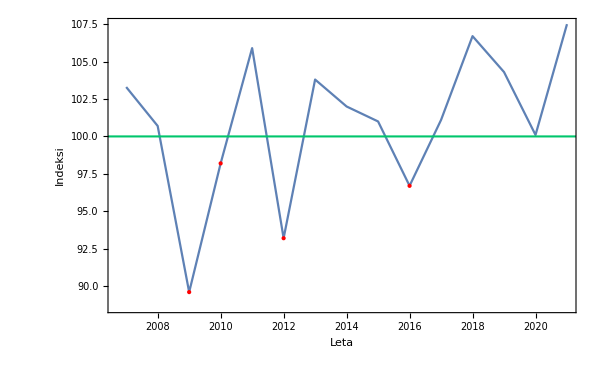

```mathematica
ListLinePlot[vsi,GridLines->{None,{100}},GridLinesStyle->Directive[AbsoluteThickness[3/2],ColorData[96,8]],Epilog->{Red,PointSize@Large,Point[{{2009,89.6},{2010,98.2},{2012,93.2},{2016,96.7}}]},Frame->True,FrameLabel->{{"Indeksi",""},{"Leta","Nove stanovanjske nepremičnine"}},BaseStyle->{FontSize->15},ImageSize->600]
```

```mathematica
yVrednosti=podatki//Transpose//Query[All,{3}]//Flatten;
```

```mathematica
(*vrednosti brez imena na začetku*)
```

```mathematica
nove=yVrednosti[[2;;]]
```

{103.3,100.7,89.6,98.2,105.9,93.2,103.8,102.,101.,96.7,101.1,106.7,104.3,100.1,107.5}

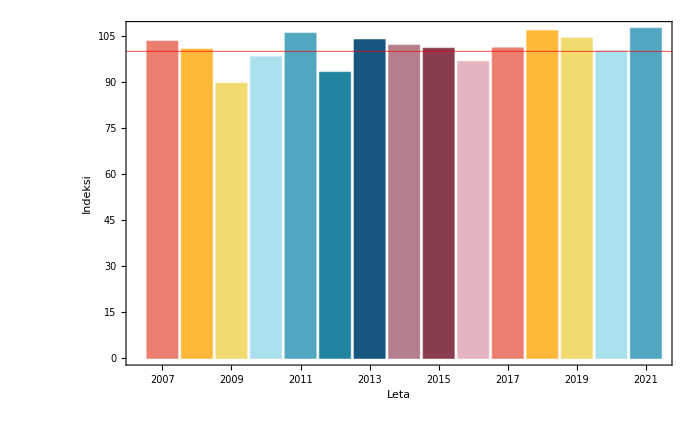

```mathematica
BarChart[{nove},ChartLabels->{leta[[2;;]]},ChartStyle->24,GridLines->{None,{100}},GridLinesStyle->Directive[Thick,Red],Frame->True,FrameLabel->{{"Indeksi",""},{"Leta","Nove stanovanjske nepremičnine"}},BaseStyle->{FontSize->14},ImageSize->700]
```

## Rabljene stanovanjske nepremičnine

```mathematica
podatki=Import[NotebookDirectory[]<>"podatki2.csv", "Table", "FieldSeparators"->";", HeaderLines->2, CharacterEncoding->"WindowsEastEurope"];
leta=podatki//First//Rest//StringTake[#,4]&//ToExpression//Prepend[#,"Leto"]&;
vsiRabljeni=podatki//Prepend[#,leta]&//Transpose//ResourceFunction["DatasetWithHeaders"]//Query[All,{1,7}]
```

```mathematica
MaximalBy[vsiRabljeni,"1.2 Rabljene stanovanjske nepremičnine"]
```

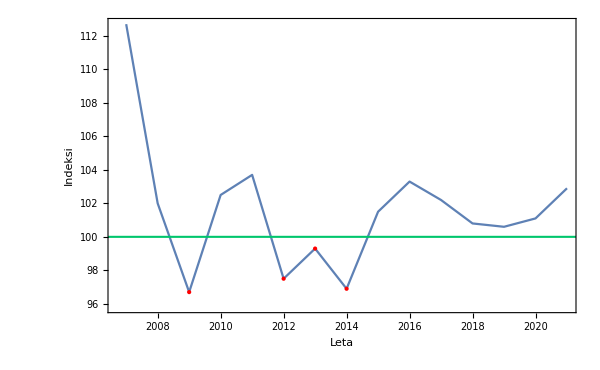

```mathematica
ListLinePlot[vsiRabljeni,GridLines->{None,{100}},GridLinesStyle->Directive[AbsoluteThickness[3/2],ColorData[96,8]],Epilog->{Red,PointSize@Large,Point[{{2009,96.7},{2012,97.5},{2013,99.3},{2014,96.9}}]},Frame->True,FrameLabel->{{"Indeksi",""},{"Leta","Rabljene stanovanjske nepremičnine"}},BaseStyle->{FontSize->15},ImageSize->600]
```

```mathematica
yVrednosti2=podatki//Transpose//Query[All,{6}]//Flatten;
```

```mathematica
nove2=yVrednosti2[[2;;]]
```

{112.7,102.,96.7,102.5,103.7,97.5,99.3,96.9,101.5,103.3,102.2,100.8,100.6,101.1,102.9}

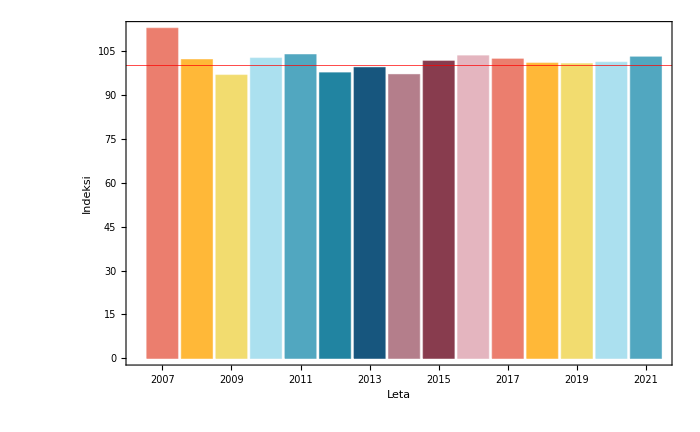

```mathematica
BarChart[{nove2},ChartLabels->{leta[[2;;]]},ChartStyle->24,GridLines->{None,{100}},GridLinesStyle->Directive[Thick,Red],Frame->True,FrameLabel->{{"Indeksi",""},{"Leta","Rabljene stanovanjske nepremičnine"}},BaseStyle->{FontSize->14},ImageSize->700]
```

## Vizualna primerjava novih in rabljenih stanovanjskih nepremičnin

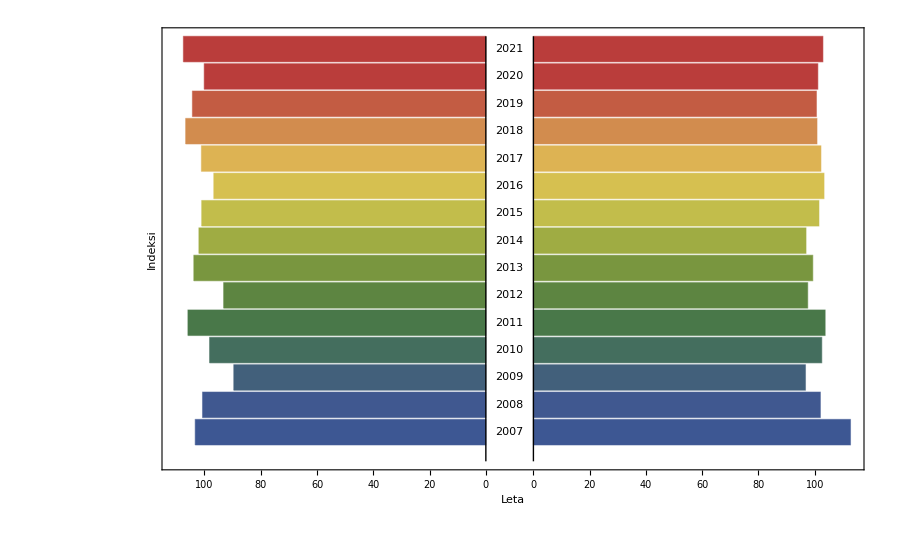

```mathematica
PairedBarChart[{nove},{nove2},ChartLabels->{leta[[2;;]]},ChartStyle->"DarkRainbow",Frame->True,FrameLabel->{{"Indeksi",""},{"Leta","Nove in rabljene stanovanjske nepremičnine"}},BaseStyle->{FontSize->14},ImageSize->900]
```

### Transponirana prvotna tabela

```mathematica
transponirana=Import[NotebookDirectory[]<>"podatki2.csv", "Table", "FieldSeparators"->";", HeaderLines->2, CharacterEncoding->"WindowsEastEurope"]//Transpose//Map[If[#=="...",0,#]&,#,{2}]&//ResourceFunction["DatasetWithHeaders"]//Query[All,<|"Leto"->ToExpression[StringTake[#"STANOVANJSKE NEPREMIČNINE",4]], #|>&]//KeyDrop["STANOVANJSKE NEPREMIČNINE"]
```

## Največji in najmanjši indeks cen za posamezno vrsto stanovanjskih nepremičnin

### Računanje največje vrednosti za posamezno vrsto nepremičnine

```mathematica
najvecjaVrednostSKUPAJ=transponirana//Normal//Query[All,"1 Stanovanjske nepremičnine - SKUPAJ"]//Max
```

109.2

```mathematica
najvecjaVrednostZaNove=transponirana//Normal//Query[All,"1.1 Nove stanovanjske nepremičnine"]//Max
```

107.5

```mathematica
najvecjaVrednostZaRabljene=transponirana//Normal//Query[All,"1.2 Rabljene stanovanjske nepremičnine"]//Max
```

112.7

### Računanje najmanjše vrednosti za posamezno vrsto nepremičnine

```mathematica
najmanjsaVrednostSKUPAJ=transponirana//Normal//Query[All,"1 Stanovanjske nepremičnine - SKUPAJ"]//Min
```

93.8

```mathematica
najmanjsaVrednostZaNove=transponirana//Normal//Query[All,"1.1 Nove stanovanjske nepremičnine"]//Min
```

89.6

```mathematica
najmanjsaVrednostZaRabljene=transponirana//Normal//Query[All,"1.2 Rabljene stanovanjske nepremičnine"]//Min
```

96.7

### Tabela največjih in najmanjših vrednosti

```mathematica
Dataset[<|"1 Stanovanjske nepremičnine - SKUPAJ"-><|"Leto"->2009,"Najmanjši indeks"->najmanjsaVrednostSKUPAJ|>,"1.1 Nove stanovanjske nepremičnine"-><|"Leto"->2009,"Najmanjši indeks"->najmanjsaVrednostZaNove|>,
"1.2 Rabljene stanovanjske nepremičnine"-><|"Leto"->2009,"Najmanjši indeks"->najmanjsaVrednostZaRabljene|>|>,DatasetTheme->{"StrongHeaders","Minimal"}]
```

```mathematica
data1=Dataset[<|"1 Stanovanjske nepremičnine - SKUPAJ"-><|"Leto"->2007,"Največji indeks"->najvecjaVrednostSKUPAJ|>,"1.1 Nove stanovanjske nepremičnine"-><|"Leto"->2021,"Največji indeks"->najvecjaVrednostZaNove|>,
"1.2 Rabljene stanovanjske nepremičnine"-><|"Leto"->2007,"Največji indeks"->najvecjaVrednostZaRabljene|>|>,DatasetTheme->{"StrongHeaders","Minimal"}]
```